```mathematica
data1={{3.00,-3.00,7.50,110.00,259.50,206.00,313.50},{2.50,-3.00,7.50,114.00,258.00,203.86,294.92},{2.00,-3.00,7.50,118.00,261.00,204.82,276.85},{1.50,-3.00,7.50,122.95,262.04,203.92,258.91},{1.00,-3.00,7.50,128.04,261.04,203.02,237.96},{0.50,-3.00,7.50,133.20,265.24,204.45,221.41},{0.00,-3.00,7.50,139.00,265.50,204.16,200.13},{-0.50,-3.00,7.50,144.08,268.54,203.00,182.00},{-1.00,-3.00,7.50,149.50,270.00,202.00,162.00},{-1.50,-3.00,7.50,155.45,272.59,203.92,144.92},{-2.00,-3.00,7.50,161.52,276.48,203.50,126.00},{-2.50,-3.00,7.50,168.10,279.10,203.50,106.00},{-3.00,-3.00,7.50,176.56,283.48,204.50,85.00},{-3.00,-2.50,7.50,176.50,261.50,197.00,89.50},{-2.50,-2.50,7.50,168.50,257.00,196.03,108.92},{-2.00,-2.50,7.50,163.00,257.50,197.00,124.50},{-1.50,-2.50,7.50,156.50,256.00,197.00,143.50},{-1.00,-2.50,7.50,151.00,253.50,197.04,160.87},{-0.50,-2.50,7.50,145.00,251.50,196.69,179.42},{0.00,-2.50,7.50,139.52,249.48,196.03,200.46},{0.50,-2.50,7.50,134.00,248.50,196.48,218.48},{1.00,-2.50,7.50,128.50,247.50,196.93,238.30},{1.50,-2.50,7.50,124.00,246.00,196.50,256.00},{2.00,-2.50,7.50,120.00,243.00,197.00,272.50},{2.50,-2.50,7.50,115.43,242.47,196.37,291.60},{3.00,-2.50,7.50,110.00,243.50,197.00,311.00},{3.00,-2.00,7.50,110.84,228.46,192.11,307.50},{2.50,-2.00,7.50,116.50,226.50,190.59,285.30},{2.00,-2.00,7.50,120.00,227.00,190.50,271.50},{1.50,-2.00,7.50,124.50,229.50,190.57,254.43},{1.00,-2.00,7.50,129.00,230.00,190.02,237.08},{0.50,-2.00,7.50,134.09,232.09,189.89,219.06},{0.00,-2.00,7.50,140.00,232.00,190.18,200.39},{-0.50,-2.00,7.50,145.08,234.11,190.07,181.07},{-1.00,-2.00,7.50,150.57,235.52,189.89,164.89},{-1.50,-2.00,7.50,157.04,238.86,191.00,145.00},{-2.00,-2.00,7.50,162.46,239.50,190.44,128.56},{-2.50,-2.00,7.50,169.52,241.52,190.01,110.07},{-3.00,-2.00,7.50,176.92,243.97,190.38,90.38},{-3.00,-1.50,7.50,177.50,225.00,183.91,92.91},{-2.50,-1.50,7.50,170.00,223.00,183.86,111.86},{-2.00,-1.50,7.50,164.50,221.50,183.00,126.00},{-1.50,-1.50,7.50,157.94,218.96,182.80,145.92},{-1.00,-1.50,7.50,152.00,220.50,184.54,162.93},{-0.50,-1.50,7.50,146.74,217.88,183.66,180.41},{0.00,-1.50,7.50,141.00,217.00,183.84,197.82},{0.50,-1.50,7.50,135.55,217.45,183.60,216.57},{1.00,-1.50,7.50,130.50,214.50,183.73,233.71},{1.50,-1.50,7.50,125.06,215.06,183.51,252.47},{2.00,-1.50,7.50,120.00,212.50,182.47,271.07},{2.50,-1.50,7.50,116.09,210.54,181.53,287.28},{3.00,-1.50,7.50,112.50,212.50,183.36,302.36},{3.00,-1.00,7.50,111.50,197.00,176.00,303.92},{2.50,-1.00,7.50,116.00,197.00,176.87,284.85},{2.00,-1.00,7.50,120.95,196.17,176.64,268.47},{1.50,-1.00,7.50,125.00,198.50,177.92,252.87},{1.00,-1.00,7.50,131.28,198.27,177.62,232.67},{0.50,-1.00,7.50,136.00,196.50,177.00,218.00},{0.00,-1.00,7.50,141.00,199.00,177.07,199.88},{-0.50,-1.00,7.50,146.29,200.14,177.33,182.37},{-1.00,-1.00,7.50,152.00,198.50,177.00,165.00},{-1.50,-1.00,7.50,158.47,200.73,177.88,147.33},{-2.00,-1.00,7.50,164.00,200.50,176.20,132.69},{-2.50,-1.00,7.50,171.41,202.36,176.56,113.41},{-3.00,-1.00,7.50,178.08,205.08,176.89,94.89},{-3.00,-0.50,7.50,178.50,185.50,171.50,97.00},{-2.50,-0.50,7.50,171.57,185.32,171.44,114.35},{-2.00,-0.50,7.50,165.50,185.00,172.00,131.00},{-1.50,-0.50,7.50,158.50,181.50,170.62,149.68},{-1.00,-0.50,7.50,153.50,183.50,171.43,163.95},{-0.50,-0.50,7.50,147.00,184.00,171.75,181.95},{0.00,-0.50,7.50,141.57,183.52,171.93,198.57},{0.50,-0.50,7.50,136.00,183.00,171.90,217.22},{1.00,-0.50,7.50,132.00,180.50,171.46,231.54},{1.50,-0.50,7.50,127.00,181.00,170.81,249.36},{2.00,-0.50,7.50,122.00,181.00,171.59,265.47},{2.50,-0.50,7.50,116.50,182.00,171.96,283.79},{3.00,-0.50,7.50,112.00,182.00,171.95,300.86},{3.00,0.00,7.50,112.00,167.00,166.39,300.44},{2.50,0.00,7.50,117.50,168.00,166.98,280.96},{2.00,0.00,7.50,122.38,166.19,166.01,265.01},{1.50,0.00,7.50,127.00,167.00,166.67,249.67},{1.00,0.00,7.50,132.00,167.50,166.75,231.74},{0.50,0.00,7.50,136.50,165.00,166.01,215.01},{0.00,0.00,7.50,142.00,167.00,166.68,199.68},{-0.50,0.00,7.50,147.50,166.00,165.69,182.69},{-1.00,0.00,7.50,154.00,165.00,165.70,164.89},{-1.50,0.00,7.50,158.50,166.00,165.97,151.61},{-2.00,0.00,7.50,166.00,165.50,165.83,132.85},{-2.50,0.00,7.50,172.20,166.61,165.30,116.30},{-3.00,0.00,7.50,179.00,166.00,165.79,99.86},{-3.00,0.50,7.50,179.21,147.33,159.00,102.50},{-2.50,0.50,7.50,172.00,148.50,160.76,118.08},{-2.00,0.50,7.50,166.00,149.00,160.28,135.19},{-1.50,0.50,7.50,159.15,149.15,159.94,151.87},{-1.00,0.50,7.50,153.70,148.88,159.79,166.92},{-0.50,0.50,7.50,148.50,150.00,159.94,181.87},{0.00,0.50,7.50,142.50,148.50,160.52,198.47},{0.50,0.50,7.50,137.75,148.72,160.08,214.20},{1.00,0.50,7.50,132.63,150.75,160.21,229.79},{1.50,0.50,7.50,127.26,151.00,161.08,247.08},{2.00,0.50,7.50,122.50,149.50,160.14,264.17},{2.50,0.50,7.50,118.34,153.39,160.63,279.69},{3.00,0.50,7.50,114.00,152.00,160.63,294.69},{3.00,1.00,7.50,113.50,139.00,155.57,295.33},{2.50,1.00,7.50,118.00,136.50,156.09,279.09},{2.00,1.00,7.50,122.50,134.50,155.30,263.34},{1.50,1.00,7.50,127.00,135.50,155.90,247.92},{1.00,1.00,7.50,132.00,134.00,155.74,231.33},{0.50,1.00,7.50,137.03,134.03,155.96,216.06},{0.00,1.00,7.50,142.50,132.50,155.40,199.80},{-0.50,1.00,7.50,148.25,131.17,155.55,183.66},{-1.00,1.00,7.50,153.50,132.00,155.53,168.47},{-1.50,1.00,7.50,159.25,129.25,155.00,154.00},{-2.00,1.00,7.50,166.50,128.98,155.32,137.08},{-2.50,1.00,7.50,172.97,128.97,155.50,119.50},{-3.00,1.00,7.50,180.00,128.00,155.42,104.05},{-3.00,1.50,7.50,180.50,110.50,151.23,106.23},{-2.50,1.50,7.50,174.43,112.91,152.00,119.00},{-2.00,1.50,7.50,166.31,112.35,150.62,137.02},{-1.50,1.50,7.50,161.00,113.50,150.45,151.45},{-1.00,1.50,7.50,155.00,114.00,151.03,167.11},{-0.50,1.50,7.50,149.57,114.00,151.00,182.00},{0.00,1.50,7.50,143.68,114.68,150.91,197.91},{0.50,1.50,7.50,138.00,117.50,150.58,214.96},{1.00,1.50,7.50,133.00,118.50,150.95,231.73},{1.50,1.50,7.50,129.00,117.50,150.50,245.17},{2.00,1.50,7.50,123.00,120.50,151.64,261.13},{2.50,1.50,7.50,118.72,119.56,150.50,276.50},{3.00,1.50,7.50,114.27,121.30,151.38,291.96},{3.00,2.00,7.50,114.73,109.60,146.00,292.00},{2.50,2.00,7.50,119.50,107.50,146.91,274.07},{2.00,2.00,7.50,123.26,106.26,147.00,260.69},{1.50,2.00,7.50,128.74,102.70,146.10,245.18},{1.00,2.00,7.50,133.27,102.51,146.19,230.06},{0.50,2.00,7.50,138.00,101.00,146.00,216.50},{0.00,2.00,7.50,143.68,98.68,146.48,199.66},{-0.50,2.00,7.50,148.50,98.00,146.04,185.97},{-1.00,2.00,7.50,154.67,96.00,146.09,169.65},{-1.50,2.00,7.50,160.17,94.97,146.04,156.36},{-2.00,2.00,7.50,166.08,93.90,146.72,140.92},{-2.50,2.00,7.50,173.49,90.36,144.98,123.98},{-3.00,2.00,7.50,180.50,90.50,145.70,107.70},{-3.00,2.50,7.50,181.59,72.50,140.50,107.50},{-2.50,2.50,7.50,174.75,74.67,141.22,123.22},{-2.00,2.50,7.50,168.59,74.36,140.82,137.41},{-1.50,2.50,7.50,161.50,78.50,141.63,153.01},{-1.00,2.50,7.50,155.90,78.90,141.15,170.00},{-0.50,2.50,7.50,150.44,81.74,141.81,183.28},{0.00,2.50,7.50,144.50,81.50,141.52,198.18},{0.50,2.50,7.50,140.00,83.00,141.75,212.20},{1.00,2.50,7.50,133.48,85.77,141.81,231.29},{1.50,2.50,7.50,128.91,87.25,141.94,243.68},{2.00,2.50,7.50,124.73,89.67,141.55,259.79},{2.50,2.50,7.50,120.13,89.39,141.36,272.97},{3.00,2.50,7.50,115.66,90.41,141.34,288.30},{3.00,3.00,7.50,115.53,75.25,137.27,287.73},{2.50,3.00,7.50,120.38,76.56,137.87,273.09},{2.00,3.00,7.50,125.00,73.00,137.30,258.77},{1.50,3.00,7.50,129.71,70.42,138.08,242.82},{1.00,3.00,7.50,134.62,70.99,137.74,229.18},{0.50,3.00,7.50,139.25,69.50,137.75,216.11},{0.00,3.00,7.50,143.26,66.50,137.00,200.50},{-0.50,3.00,7.50,149.00,65.00,137.00,186.50},{-1.00,3.00,7.50,155.13,63.76,137.30,171.49},{-1.50,3.00,7.50,160.52,60.48,136.69,157.92},{-2.00,3.00,7.50,167.09,56.94,136.39,141.71},{-2.50,3.00,7.50,174.23,55.39,136.35,126.01},{-3.00,3.00,7.50,181.50,51.50,136.27,110.31}};
data2={{3.00,-3.00,11.56,225.00,255.00,343.21,299.53},{2.00,-3.00,11.56,237.00,256.00,340.50,264.50},{1.00,-3.00,11.56,249.00,258.00,340.00,231.50},{0.00,-3.00,11.56,263.00,261.00,340.03,198.17},{-1.00,-3.00,11.56,277.00,265.50,339.70,164.00},{-2.00,-3.00,11.56,293.13,270.79,339.89,130.09},{-3.00,-3.00,11.56,312.00,275.50,340.00,93.50},{-3.00,-2.00,11.56,312.03,238.04,321.30,99.89},{-2.00,-2.00,11.56,296.39,237.88,322.78,129.91},{-1.00,-2.00,11.56,279.78,233.00,321.96,163.06},{0.00,-2.00,11.56,263.24,231.57,323.29,198.09},{1.00,-2.00,11.56,249.79,228.29,321.94,231.04},{2.00,-2.00,11.56,237.64,226.46,322.50,260.50},{3.00,-2.00,11.56,226.50,224.00,324.00,292.50},{3.00,-1.00,11.56,226.97,197.25,306.97,290.50},{2.00,-1.00,11.56,239.00,197.50,307.09,260.13},{1.00,-1.00,11.56,251.79,198.90,306.50,228.00},{0.00,-1.00,11.56,265.12,199.42,306.00,197.50},{-1.00,-1.00,11.56,279.49,200.41,305.14,166.12},{-2.00,-1.00,11.56,296.94,202.06,305.00,132.00},{-3.00,-1.00,11.56,314.50,204.00,305.12,101.69},{-3.00,0.00,11.56,314.73,169.41,289.23,104.98},{-2.00,0.00,11.56,298.00,168.50,290.68,134.06},{-1.00,0.00,11.56,282.13,168.46,290.28,164.98},{0.00,0.00,11.56,267.00,167.50,290.95,195.25},{1.00,0.00,11.56,252.40,170.22,291.40,225.60},{2.00,0.00,11.56,239.45,168.78,291.50,257.00},{3.00,0.00,11.56,226.50,169.50,292.57,289.37},{3.00,1.00,11.56,228.65,141.54,278.82,283.27},{2.00,1.00,11.56,239.72,142.79,278.39,256.59},{1.00,1.00,11.56,253.00,140.00,277.67,226.47},{0.00,1.00,11.56,266.97,138.01,276.50,196.50},{-1.00,1.00,11.56,282.37,137.30,276.50,168.50},{-2.00,1.00,11.56,298.38,136.46,276.00,137.50},{-3.00,1.00,11.56,315.00,135.00,275.87,109.93},{-3.00,2.00,11.56,315.86,104.14,264.50,112.29},{-2.00,2.00,11.56,298.52,104.63,263.60,140.40},{-1.00,2.00,11.56,283.00,106.00,263.60,167.60},{0.00,2.00,11.56,268.54,107.51,263.00,195.00},{1.00,2.00,11.56,254.34,110.50,264.37,224.12},{2.00,2.00,11.56,241.39,112.59,264.59,252.41},{3.00,2.00,11.56,229.89,114.58,264.00,281.00},{3.00,3.00,11.56,229.00,85.50,251.81,279.55},{2.00,3.00,11.56,242.23,85.49,253.33,251.67},{1.00,3.00,11.56,254.00,81.00,251.93,224.26},{0.00,3.00,11.56,266.50,77.50,251.66,199.33},{-1.00,3.00,11.56,283.44,73.69,250.71,169.57},{-2.00,3.00,11.56,300.50,71.50,250.76,142.05},{-3.00,3.00,11.56,318.70,68.77,251.00,114.50}};
data3={{3.00,-3.00,15.00,307.25,249.43,434.28,290.30},{2.00,-3.00,15.00,320.90,249.10,433.00,261.00},{1.00,-3.00,15.00,335.39,254.44,434.12,227.57},{0.00,-3.00,15.00,352.00,256.00,432.50,195.50},{-1.00,-3.00,15.00,367.45,261.20,434.00,165.50},{-2.00,-3.00,15.00,384.84,264.00,432.50,135.00},{-3.00,-3.00,15.00,405.03,271.00,433.57,102.44},{-3.00,-2.00,15.00,405.16,236.95,412.50,106.00},{-2.00,-2.00,15.00,387.00,234.50,413.09,135.02},{-1.00,-2.00,15.00,369.89,231.89,414.17,164.07},{0.00,-2.00,15.00,353.15,228.50,413.93,195.43},{1.00,-2.00,15.00,337.06,225.78,413.75,225.59},{2.00,-2.00,15.00,322.60,223.93,414.16,255.12},{3.00,-2.00,15.00,309.50,223.00,415.03,285.06},{3.00,-1.00,15.00,309.00,197.50,397.00,283.50},{2.00,-1.00,15.00,322.53,198.07,396.22,255.00},{1.00,-1.00,15.00,337.42,199.20,396.41,225.59},{0.00,-1.00,15.00,353.41,200.41,396.00,195.50},{-1.00,-1.00,15.00,370.29,201.41,395.50,166.00},{-2.00,-1.00,15.00,388.50,203.00,394.92,136.83},{-3.00,-1.00,15.00,406.57,204.39,394.05,108.96},{-3.00,0.00,15.00,407.39,173.60,377.50,111.50},{-2.00,0.00,15.00,389.19,171.38,377.07,138.07},{-1.00,0.00,15.00,371.00,172.53,378.71,166.84},{0.00,0.00,15.00,354.00,171.38,378.79,193.85},{1.00,0.00,15.00,339.14,171.02,378.50,223.00},{2.00,0.00,15.00,323.47,171.00,379.96,252.62},{3.00,0.00,15.00,309.61,171.69,380.55,280.69},{3.00,1.00,15.00,310.50,146.50,365.57,277.22},{2.00,1.00,15.00,324.63,145.00,363.90,249.76},{1.00,1.00,15.00,339.18,143.89,362.00,222.50},{0.00,1.00,15.00,355.19,142.73,362.47,195.47},{-1.00,1.00,15.00,371.26,141.81,362.50,169.50},{-2.00,1.00,15.00,388.00,141.50,361.48,142.40},{-3.00,1.00,15.00,408.00,141.00,361.60,115.40},{-3.00,2.00,15.00,410.12,111.12,347.68,116.11},{-2.00,2.00,15.00,391.00,112.50,347.46,141.90},{-1.00,2.00,15.00,373.00,112.50,347.41,168.09},{0.00,2.00,15.00,355.04,114.46,347.76,194.76},{1.00,2.00,15.00,340.65,115.89,347.00,220.00},{2.00,2.00,15.00,326.70,118.30,348.00,247.00},{3.00,2.00,15.00,312.41,120.41,348.88,273.50},{3.00,3.00,15.00,312.06,92.50,333.50,271.50},{2.00,3.00,15.00,325.85,91.92,335.02,246.98},{1.00,3.00,15.00,339.75,90.38,335.50,221.50},{0.00,3.00,15.00,355.87,86.32,334.38,196.23},{-1.00,3.00,15.00,373.50,84.50,334.53,169.54},{-2.00,3.00,15.00,391.50,82.00,333.50,144.50},{-3.00,3.00,15.00,412.98,78.14,333.50,118.50}};
data4={{3.00,-3.00,18.06,373.50,247.50,507.00,283.60},{2.00,-3.00,18.06,387.50,247.00,503.87,255.56},{1.00,-3.00,18.06,403.67,250.45,504.50,225.00},{0.00,-3.00,18.06,420.82,252.39,503.92,196.06},{-1.00,-3.00,18.06,437.86,255.77,503.00,168.00},{-2.00,-3.00,18.06,457.50,259.50,503.87,137.74},{-3.00,-3.00,18.06,478.16,263.51,503.05,109.05},{-3.00,-2.00,18.06,479.00,234.50,482.57,112.00},{-2.00,-2.00,18.06,459.55,232.55,483.05,138.20},{-1.00,-2.00,18.06,440.54,228.53,483.00,166.50},{0.00,-2.00,18.06,422.58,225.16,482.32,195.32},{1.00,-2.00,18.06,405.53,223.54,483.50,222.00},{2.00,-2.00,18.06,389.55,221.96,483.57,251.43},{3.00,-2.00,18.06,375.46,220.46,483.44,278.50},{3.00,-1.00,18.06,375.58,196.92,465.00,277.00},{2.00,-1.00,18.06,390.31,197.31,464.54,250.40},{1.00,-1.00,18.06,406.43,199.50,465.50,222.00},{0.00,-1.00,18.06,423.02,199.98,464.50,195.50},{-1.00,-1.00,18.06,440.73,200.65,463.84,168.22},{-2.00,-1.00,18.06,459.91,202.40,463.00,141.50},{-3.00,-1.00,18.06,481.00,204.00,463.46,113.46},{-3.00,0.00,18.06,482.08,174.00,445.00,116.00},{-2.00,0.00,18.06,461.10,172.02,444.37,142.59},{-1.00,0.00,18.06,442.50,173.00,445.58,168.44},{0.00,0.00,18.06,423.66,172.83,446.02,195.02},{1.00,0.00,18.06,407.00,172.50,446.55,220.11},{2.00,0.00,18.06,390.50,171.50,446.28,248.16},{3.00,0.00,18.06,376.47,172.46,447.88,273.88},{3.00,1.00,18.06,376.50,149.00,430.55,271.33},{2.00,1.00,18.06,391.50,148.50,430.27,245.73},{1.00,1.00,18.06,407.73,146.13,429.50,221.00},{0.00,1.00,18.06,425.48,145.80,429.08,194.92},{-1.00,1.00,18.06,444.34,144.69,429.00,170.50},{-2.00,1.00,18.06,464.34,144.35,428.83,143.95},{-3.00,1.00,18.06,482.57,144.44,428.10,118.94},{-3.00,2.00,18.06,483.50,116.00,412.86,120.43},{-2.00,2.00,18.06,464.26,117.98,413.87,144.45},{-1.00,2.00,18.06,445.91,117.31,412.95,169.48},{0.00,2.00,18.06,427.27,117.89,414.50,194.50},{1.00,2.00,18.06,409.50,122.50,415.00,219.00},{2.00,2.00,18.06,393.54,123.47,414.77,243.77},{3.00,2.00,18.06,378.19,124.31,414.91,266.91},{3.00,3.00,18.06,379.88,98.99,399.50,265.50},{2.00,3.00,18.06,394.57,98.53,400.94,241.94},{1.00,3.00,18.06,411.47,96.47,400.23,219.09},{0.00,3.00,18.06,429.00,92.50,399.00,194.50},{-1.00,3.00,18.06,445.20,90.93,399.28,170.87},{-2.00,3.00,18.06,462.00,91.00,399.23,148.09},{-3.00,3.00,18.06,482.26,86.99,398.00,125.50}};
data= Join[data1,data2,data3,data4];
```

837.064

{ec1x→-0.350092,ec1y→-0.878546,ec1z→0.838027,ec2x→-0.253576,ec2y→-0.275261,ec2z→0.00152631,ec1ϕ→-3.12009,ec2ϕ→-1.56957,ec1θ→0.851343,ec2θ→2.14801,ec1γ→-1.80135,ec2γ→-0.558503,ecx→14.7714,ecy→-4.28098,efx→-24.9929,efy→-29.0805}

c1toGlobal = [[-0.546532, -0.00232285, 0.837435, -20.8501], [0.0233164, -0.999651, 0.0124441, -0.128546], [0.837113, 0.0263271, 0.546396, 0.838027], [0., 0., 0., 1.]]
c2toGlobal = [[0.00988099, 0.999441, -0.0319341, -0.253576], [-0.523506, 0.0323798, 0.851406, -20.7753], [0.851965, 0.00830498, 0.523534, 0.751526], [0., 0., 0., 1.]]
fx = 725.902
fy = 706.294
cx = 341.759
cy = 166.322

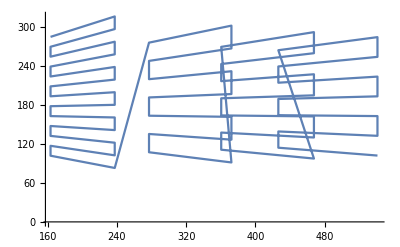

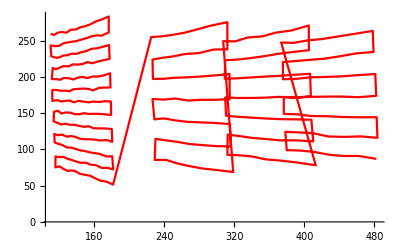

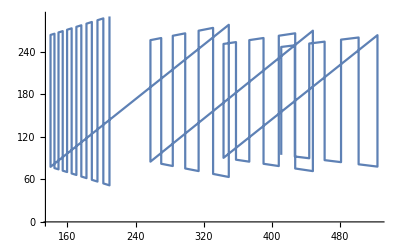

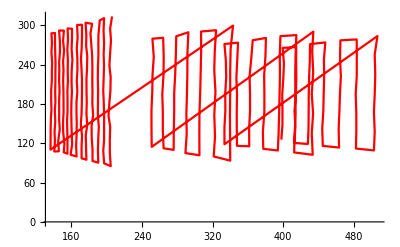

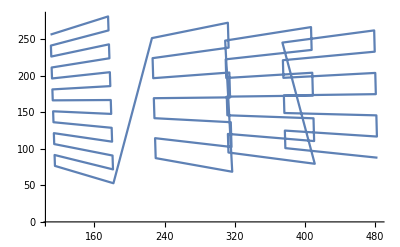

-Graphics-

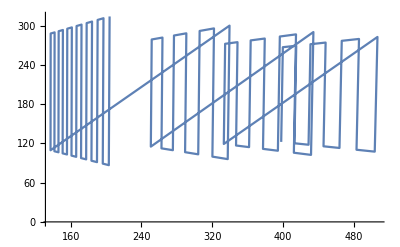

-Graphics-

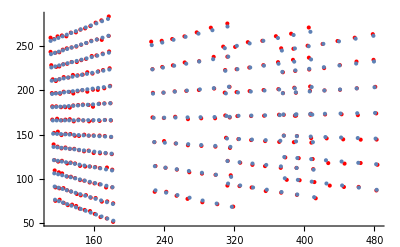

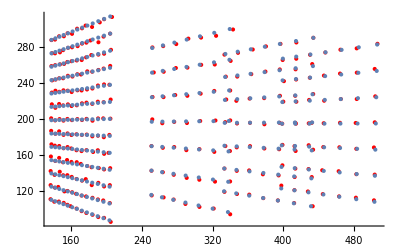

```mathematica
args = {ec1x,ec1y,ec1z,ec2x,ec2y,ec2z,ec1ϕ,ec2ϕ,ec1θ,ec2θ,ec1γ,ec2γ,ecx,ecy,efx,efy};
assigns={};
perfect = #->0&/@args;
c1Pos={-20.5+ec1x,.75+ec1y,ec1z,1};
c2Pos={ec2x,-20.5+ec2y,.75+ec2z,1};
c1ϕ=π/3+ec1ϕ Degree;
c2ϕ=π/3+ec2ϕ Degree;
c1θ=0+ec1θ Degree;
c2θ=π/2+ec2θ Degree;
c1γ=ec1γ Degree;
c2γ=ec2γ Degree;
fx=750.89501953125+efx;
fy= 735.374755859375+efy;
cx = 326.98767770128325+ecx;
cy=170.60347574188199+ecy;
project[{x_,y_,z_,w_}]:={fx*x/z+cx,fy*y/z+cy}

c1k={Sin[c1ϕ]Cos[c1θ],Sin[c1ϕ]Sin[c1θ],Cos[c1ϕ]};
c2k={Sin[c2ϕ]Cos[c2θ],Sin[c2ϕ]Sin[c2θ],Cos[c2ϕ]};
c1iTrue={Sin[c1ϕ-π/2]Cos[c1θ],Sin[c1ϕ-π/2]Sin[c1θ],Cos[c1ϕ-π/2]};
c2iTrue={Sin[c2ϕ-π/2]Cos[c2θ],Sin[c2ϕ-π/2]Sin[c2θ],Cos[c2ϕ-π/2]};
c1jTrue=-Cross[c1iTrue,c1k];
c2jTrue=-Cross[c2iTrue,c2k];
c1i=Cos[c1γ]c1iTrue+Sin[c1γ]c1jTrue;
c2i=Cos[c2γ]c2iTrue+Sin[c2γ]c2jTrue;
c1j=-Sin[c1γ]c1iTrue+Cos[c1γ]c1jTrue;
c2j=-Sin[c2γ]c2iTrue+Cos[c2γ]c2jTrue;

tmat[{x_,y_,z_,w_}]:={{1,0,0,x},{0,1,0,y},{0,0,1,z},{0,0,0,1}}
frameMat[i_,j_,k_,pos_]:={i~Join~{0},j~Join~{0},k~Join~{0},{0,0,0,1}}.tmat[-pos];

c1Frame = frameMat[c1i,c1j,c1k,c1Pos];
c2Frame=frameMat[c2i,c2j,c2k,c2Pos];
c1FramePosition[x_,y_,z_]:=c1Frame.{x,y,z,1}
c2FramePosition[x_,y_,z_]:=c2Frame.{x,y,z,1}

c1[{x_,y_,z_}]:=project[c1FramePosition[x,y,z]]
c2[{x_,y_,z_}]:=project[c2FramePosition[x,y,z]]

pts3d = data[[All,1;;3]];
ptsc1=data[[All,4;;5]];
ptsc2=data[[All,6;;7]];
calculated = (c1/@pts3d)~Join~(c2/@pts3d);
measured = ptsc1~Join~ptsc2;
cost =Total[ Norm/@(calculated-measured)];
(*{minCost,sol}=Minimize[cost/.assigns,args];*)
minCost
sol
"c1toGlobal = "<>StringReplace[Inverse[c1Frame/.sol]//ToString,{"{"->"[","}"->"]"}]<>"\n"<>
"c2toGlobal = "<>StringReplace[Inverse[c2Frame/.sol]//ToString,{"{"->"[","}"->"]"}]<>"\n"<>
"fx = "<>StringReplace[fx/.sol//ToString,{"{"->"[","}"->"]"}]<>"\n"<>
"fy = "<>StringReplace[fy/.sol//ToString,{"{"->"[","}"->"]"}]<>"\n"<>
"cx = "<>StringReplace[cx/.sol//ToString,{"{"->"[","}"->"]"}]<>"\n"<>
"cy = "<>StringReplace[cy/.sol//ToString,{"{"->"[","}"->"]"}]

ListLinePlot[c1/@pts3d/.assigns/.perfect]
ListLinePlot[ptsc1,PlotStyle->Red]
ListLinePlot[c2/@pts3d/.assigns/.perfect]
ListLinePlot[ptsc2,PlotStyle->Red]
ListLinePlot[c1/@pts3d/.assigns/.sol]
ListLinePlot[ptsc1,PlotStyle->Red]
ListLinePlot[c2/@pts3d/.assigns/.sol]
ListLinePlot[ptsc2,PlotStyle->Red]
Show[{ListPlot[ptsc1,PlotStyle->Red],
ListPlot[c1/@pts3d/.assigns/.sol]},PlotRange->All]
Show[{ListPlot[ptsc2,PlotStyle->Red],
ListPlot[c2/@pts3d/.assigns/.sol]},PlotRange->All]
```